-Graphics-  Badges indicate graded exercises for certification

Use Prime and Array to generate a list of the first 100 primes.

EXPECTED OUTPUT »

```mathematica
Array[Prime[#] &, 100]
```

Use Prime and Array to find successive differences between the first 100 primes.

EXPECTED OUTPUT »

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

```mathematica
Array[Prime[#+1] - Prime[#] &, 100]
```

Use Array and Grid to make a 10 by 10 addition table.

EXPECTED OUTPUT »

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
Array[Plus,{10,10}] // Grid
```

Use Array to make a 10 by 10 grid where the leading diagonal and everything below it is 1 and the rest is 0.

EXPECTED OUTPUT »

```mathematica
Array[If[#1 ≥#2,1,0] &, {10,10}] // Grid
```

Use FoldList, Times and Range to successively multiply numbers up to 10 (making factorials).

EXPECTED OUTPUT »

```mathematica
FoldList[Times,1, Range[10]]
```

Use FoldList and Array to compute the successive products of the first 10 primes.

EXPECTED OUTPUT »

```mathematica
FoldList[Times,1,Array[Prime[#] &,10]]
```

Use FoldList to successively ImageAdd regular polygons with between 3 and 8 sides, and with opacity 0.2.

EXPECTED OUTPUT »

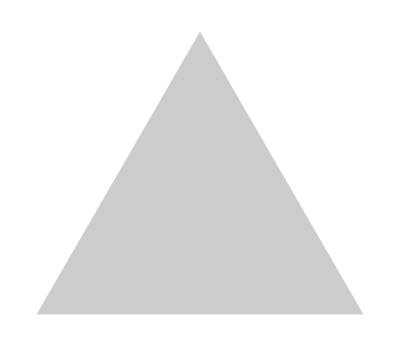
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd, Table[Graphics[{Opacity[0.2],RegularPolygon[n]}],{n, Range[3,8]}]]
```